```mathematica
ya[x_] := 2;
yw[x_] :=1/4 Sin[1/2 π (x+1)];
```

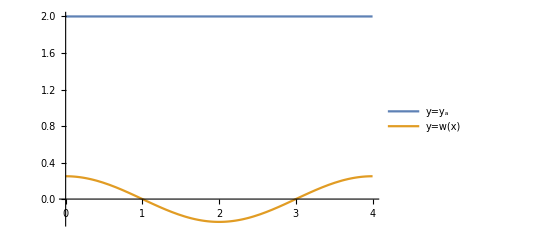

```mathematica
plMain=Plot[{ya[x],yw[x]},{x,0,4},PlotStyle->{Thick,Thick},PlotLegends->{HoldForm[y=Subscript[y, a]],HoldForm[y=w[x]]}]
```

```mathematica
plLeftRightLine=ListLinePlot[{{{0,-0.2},{0,2.2}}, {{4,-0.2},{4,2.2}}},PlotStyle->{{Dashed,Darker@Red},{Dashed,Darker@Red}}];
```

```mathematica
plLeftEnds=Plot[{ya[x],yw[x]},{x,-0.5,0},PlotStyle->{{Dashed, Thickness->0.006},{Dashed, Thickness->0.006}}];
plRightEnds=Plot[{ya[x],yw[x]},{x,4,4.5},PlotStyle->{{Dashed, Thickness->0.006},{Dashed, Thickness->0.006}}];
```

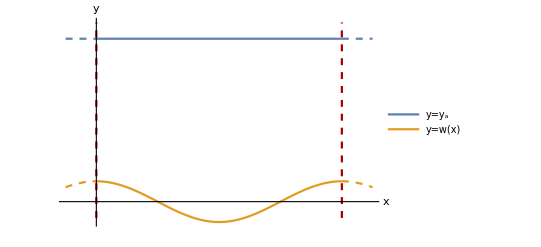

```mathematica
exp1=Show[{plMain, plLeftRightLine, plLeftEnds, plRightEnds}, PlotRange->Full,AxesLabel->{Style[HoldForm[x],FontSize->14 ,Black],Style[HoldForm[y],FontSize->14, Black]},AxesStyle->{{Directive[Arrowheads[Small]], Black}, {Directive[Arrowheads[Small]], Black}},Ticks->None]
```

```mathematica
Export["/home/san/Code/2d_Laplace_eq_FEM/latex/illustr/illustr.pdf",exp1]
```

/home/san/Code/2d_Laplace_eq_FEM/latex/illustr/illustr.pdf